## somethings wrong--how can it take fewer than one cycle to heat the atom out?????

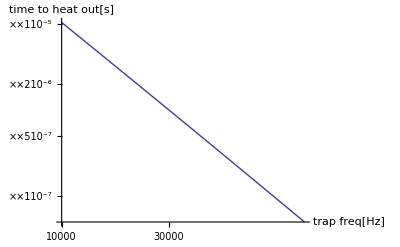

```mathematica
Clear["Global`*"]
Ttr =1.6 10^-3;(*trap depth in K*)
kB=1.38 10^-23;
h= 6.63 10^-34;
nTot = (kB Ttr)/(h ftr);
ϵ0=.1/2;(*5% intensity modulation*)
S=1/π ϵ0^2; 
(*from paper: S = Integral of ϵ0^2 over Bandwidth of noise in Hz (real freq)*)
T=1/(π^2(ftr)^2 S);
LogLogPlot[T Log[nTot],{ftr,10 10^3,120 10^3},AxesLabel->{"trap freq[Hz]","time to heat out[s]"},PlotRange->All]
```

```mathematica
10^6 1/(π^2(10 10^3)^2(.05)^2/100)
```

40.5285

```mathematica
10^6/(10 10^3)
```

100

## heating time scales as 1/(e0^2 ftrap^2) (numbers from hansch)

```mathematica
ftr=2 10^3;
ϵ0=0.3;
fmod=2 ftr;
s=Solve[1000/fmod==A/((ϵ0)^2(ftr)^2) ,A][[1]]
```

{A→90000.}

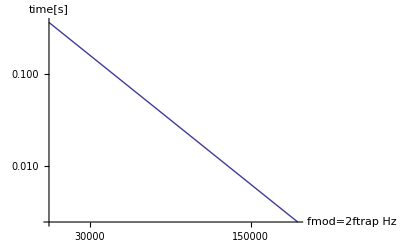

```mathematica
Clear[fmod]
LogLogPlot[A/((0.05)^2(fmod/2)^2)/.s,{fmod,20 10^3,240 10^3},PlotRange->All,AxesLabel->{"fmod=2ftrap Hz","time[s]"}]
```